```mathematica
Clear[resperado]
condiciones={a->1}
resperado[n_,l_] := (1 + 1/2(1 - (l(l+1))/n^2) )n^2
```

{a→1}

```mathematica
resperado[1,0]
resperado[2,0]
resperado[3,0]
resperado[3,1]
resperado[3,2]
```

3/2

6

27/2

25/2

21/2

```mathematica
R10=2/(√(a^3))Exp[- r/a]
R20=√(2/a)(1/(2a))(1- r/(2a))Exp[-r/(2a)]
R21=√(1/(6a))(1/(2 a^2))r Exp[-r/(2a)]
R30=2/(√27)a^(-3/2)(1-(2r)/(3a)+2/27(r/a)^2)Exp[-r/(3a)]
R31=8/(27 √6)a^(-3/2)(1-r/(6a))(r/a)Exp[-r/(3a)]
R32=4/(81 √30)a^(-3/2)(r/a)^2 Exp[-r/(3a)]
```

(2 ⅇ^(-r/a))/(√(a^3))

((1/a)^(3/2) ⅇ^(-r/(2 a)) (1-r/(2 a)))/(√2)

((1/a)^(5/2) ⅇ^(-r/(2 a)) r)/(2 √6)

(2 ⅇ^(-r/(3 a)) (1-(2 r)/(3 a)+(2 r^2)/(27 a^2)))/(3 √3 a^(3/2))

(4 √(2/3) ⅇ^(-r/(3 a)) r (1-r/(6 a)))/(27 a^(5/2))

(2 √(2/15) ⅇ^(-r/(3 a)) r^2)/(81 a^(7/2))

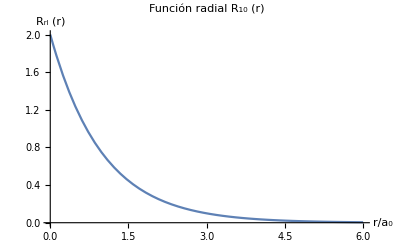

```mathematica
Plot[R10/.condiciones,{r,0,6},PlotRange->All,PlotLabel->Style["Función radial R_10 (r)",FontSize->16,Black],AxesLabel->{Style["r/a_0",14,Black],Style["R_rl (r)",14,Black]}]
```

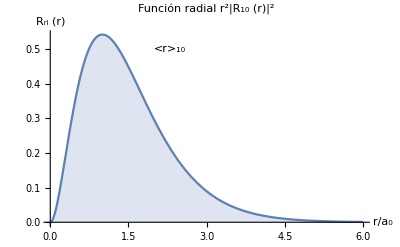

```mathematica
Plot[r^2 Abs[R10/.condiciones]^2,{r,0,6},PlotRange->All,PlotLabel->Style["Función radial r^2|R_10 (r)|^2",FontSize->16,Black],AxesLabel->{Style["r/a_0",14,Black],Style["R_rl (r)",14,Black]},Filling->Axis,GridLines->{{resperado[1,0]},{}},GridLinesStyle->Directive[Thickness[Large],Red, Dashed],Epilog->Style[Text["<r>_10",{2.3,0.5}],16]]
```

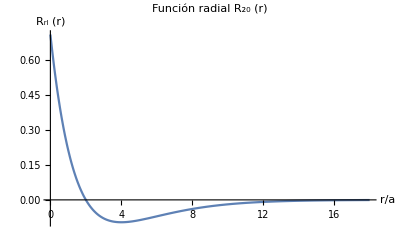

```mathematica
Plot[R20/.condiciones,{r,0,18},PlotRange->All,PlotLabel->Style["Función radial R_20 (r)",FontSize->16,Black],AxesLabel->{Style["r/a",14,Black],Style["R_rl (r)",14,Black]}]
```

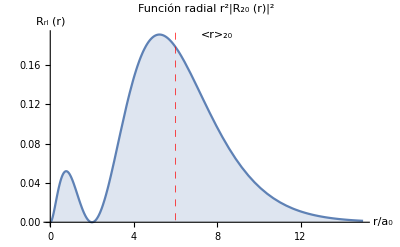

```mathematica
Plot[r^2 Abs[R20/.condiciones]^2,{r,0,15},PlotRange->All,PlotLabel->Style["Función radial r^2|R_20 (r)|^2",FontSize->16,Black],AxesLabel->{Style["r/a_0",14,Black],Style["R_rl (r)",14,Black]},Filling->Axis, GridLines->{{resperado[2,0]},{}},GridLinesStyle->Directive[Thickness[Large],Red, Dashed],Epilog->Style[Text["<r>_20",{8,0.19}],16]]
```

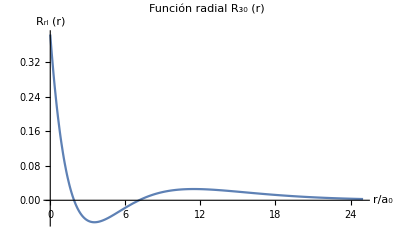

```mathematica
Plot[R30/.condiciones,{r,0,25},PlotRange->All,PlotLabel->Style["Función radial R_30 (r)",FontSize->16,Black],AxesLabel->{Style["r/a_0",14,Black],Style["R_rl (r)",14,Black]}]
```

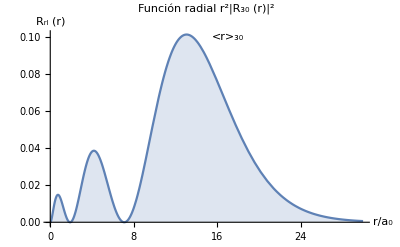

```mathematica
Plot[r^2 Abs[R30/.condiciones]^2,{r,0,30},PlotRange->All,PlotLabel->Style["Función radial r^2|R_30 (r)|^2",FontSize->16,Black],AxesLabel->{Style["r/a_0",14,Black],Style["R_rl (r)",14,Black]},Filling->Axis, GridLines->{{resperado[3,0]},{}},GridLinesStyle->Directive[Thickness[Large],Red, Dashed],Epilog->Style[Text["<r>_30",{17,0.1}],16]]
```

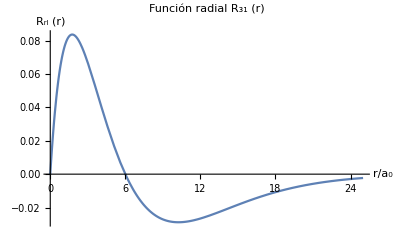

```mathematica
Plot[R31/.condiciones,{r,0,25},PlotRange->All,PlotLabel->Style["Función radial R_31 (r)",FontSize->16,Black],AxesLabel->{Style["r/a_0",14,Black],Style["R_rl (r)",14,Black]}]
```

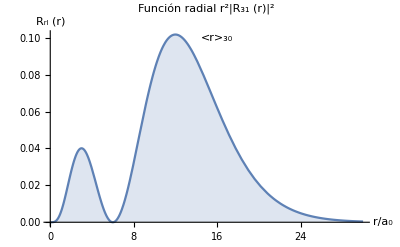

```mathematica
Plot[r^2 Abs[R31/.condiciones]^2,{r,0,30},PlotRange->All,PlotLabel->Style["Función radial r^2|R_31 (r)|^2",FontSize->16,Black],AxesLabel->{Style["r/a_0",14,Black],Style["R_rl (r)",14,Black]},Filling->Axis, GridLines->{{resperado[3,1]},{}},GridLinesStyle->Directive[Thickness[Large],Red, Dashed],Epilog->Style[Text["<r>_30",{16,0.1}],16]]
```

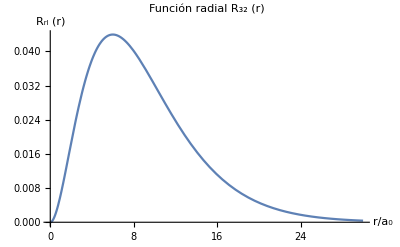

```mathematica
Plot[R32/.condiciones,{r,0,30},PlotRange->All,PlotLabel->Style["Función radial R_32 (r)",FontSize->16,Black],AxesLabel->{Style["r/a_0",14,Black],Style["R_rl (r)",14,Black]}]
```

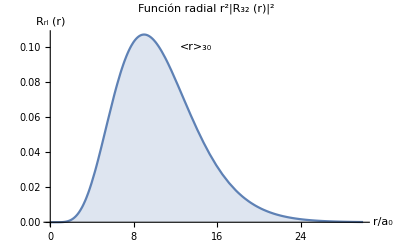

```mathematica
Plot[r^2 Abs[R32/.condiciones]^2,{r,0,30},PlotRange->All,PlotLabel->Style["Función radial r^2|R_32 (r)|^2",FontSize->16,Black],AxesLabel->{Style["r/a_0",14,Black],Style["R_rl (r)",14,Black]},Filling->Axis, GridLines->{{resperado[3,2]},{}},GridLinesStyle->Directive[Thickness[Large],Red, Dashed],Epilog->Style[Text["<r>_30",{14,0.1}],16]]
```